# Define functions and module for general ODE

```mathematica
(*kval=1.5;
bv = bmax*(x^2-1);(* quadratic basal topography*)
eqiceODE = (ρ-1)(D[H[x],x]+D[bv,x]) - 0.5*((α-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*α))*H[x]  -ρ*((kval*Abs[b0]-b0) - H[x]-bv+ x*α)*(fλ/H[x]+D[bv,x,x]*(α/(1+D[bv,x]*α)-D[bv,x]/ (1+(D[bv,x])^2)))==fλ + ρ *α-(α-D[bv,x])/(1+D[bv,x]*α);
(*define function to find landslide toe*)
xPosRoot[ρv_?NumericQ,αv_?NumericQ,fv_?NumericQ, b0_?NumericQ]:=Module[{sol,res,xend,H},
xend=0.0;sol=Quiet@Check[NDSolve[{eqiceODE/.{ρ->ρv,bmax->b0,α->αv,fλ->fv},H[0]==kval*Abs[b0],WhenEvent[H[x]<=0.0001,{xend=x,"StopIntegration"}]},H,{x,0,1}],$Failed];
If[sol===$Failed,0.0,(*fallback if solve fails*)
res=xend
]
]
(*locusfun[ρ_,f_,b0_,k_]:=Module[{res},res=
Quiet@FindRoot[xPosRoot[ρ,αsol,f,b0,k]==1.0,{αsol,0.0,0,10}];
αsol/. res]*)
xPosRoot[0.1,0.4,0.45,0.1]*)
```

```mathematica
(*Helper:solve the H ODE and return InterpolatingFunction or $Failed*)
ClearAll[solveH,xPosRoot,locusPosFun];
solveH[ρ_?NumericQ,α_?NumericQ,f_?NumericQ,b0_?NumericQ,k_?NumericQ,{xmin_?NumericQ,xmax_?NumericQ}]:=Module[{bv,dbv,dbv2,eq,sol,Hfun,tiny=10^-4},(*analytic basal shape and derivatives (quadratic)*)
bv[x_]:=b0*(x^2-1);
dbv[x_]:=2 b0 x;
dbv2[x_]:=2 b0;
(*equation written with x as the independent variable*)eq=(ρ-1) (D[H[x],x]+dbv[x])-0.5*((α-dbv[x])/(1+dbv[x]^2)*dbv2[x]/(1+dbv[x] α))*H[x]-ρ*(k*Abs[b0]-H[x]-bv[x]+x*α)*(f/H[x]+dbv2[x]*(α/(1+dbv[x] α)-dbv[x]/(1+dbv[x]^2)))==f+ρ*α-(α-dbv[x])/(1+dbv[x] α);
(*Solve with NDSolve;place WhenEvent to stop if H becomes tiny*)sol=Quiet[Check[NDSolve[{eq,H[0]==k*Abs[b0],WhenEvent[H[x]<=tiny,{"StopIntegration"}]},H,{x,xmin,xmax},MaxSteps->Infinity (*optional,helps convergence sometimes*)],$Failed]];
If[sol===$Failed,$Failed,(*return the InterpolatingFunction for H*)
Hfun=H/. First[sol];
Hfun]];

(*xPosRoot:find positive root (toe) using the H solution*)
xPosRoot[ρ_?NumericQ,α_?NumericQ,f_?NumericQ,b0_?NumericQ,k_?NumericQ]:=Module[{Hfun,guess,root},
Hfun=solveH[ρ,α,f,b0,k,{0.,1.}];
(*If[Hfun===$Failed,1.0,(*fallback if solve fails*)
Quiet@Check[root=x/.Last[FindRoot[((H[x]/. Hfun)==0),{x,0.9,0,1}]],0]
]*)
If[Hfun===$Failed,Return[1.0]];(*fallback if solver fails*)(*try FindRoot near the toe;but first guard by sign check*)
Check[(guess=0.9;(*initial guess near toe*)root=Quiet@Check[x/. FindRoot[Hfun[x]==0,{x,guess,0.0,1.}],(*bracketed search*)(*fallback try with single-start guess*)
x/. FindRoot[Hfun[x]==0,{x,guess}]];
(*if root is not in[0,1] then clamp or return 1.0*)If[NumericQ[root]&&0<=root<=1,root,1.0]),
(*on any error,return fallback*)
0.0]
];

(*locusPosFun[f_?NumericQ,b0_?NumericQ,k_?NumericQ,ρ_?NumericQ]:=Module[{res},res=Quiet@FindRoot[xPosRoot[ρ,αsol,f,b0,k]==0.95,
{αsol,0.0,0,10}];
αsol/. res];*)
locusPosFun[f_?NumericQ,b0_?NumericQ,k_?NumericQ,ρ_?NumericQ]:=Module[{αgrid,xvals,target=0.99,bestα},
(*coarse grid of alpha values to scan*)
αgrid=Range[0.,3.,0.01];
(*evaluate xPosRoot at each alpha*)
xvals=Table[Quiet[xPosRoot[ρ,α,f,b0,k]],{α,αgrid}];
(*pick alpha giving xPosRoot closest to the target*)bestα=First@First@SortBy[Transpose[{αgrid,Abs[xvals-target]}],Last];
bestα
]
(*Check if function works*)
xPosRoot[0.1,0.59,0.2,0.2,1]
locusPosFun[0.2,0.2,1,0.1]
```

0.998197

0.58

## Insert values for a test case

```mathematica
(*αv=0.4;
fv=0.45;
b0=0.1;
ρi = 0.1;
xPosRoot[ρi,αv,fv,b0]
xendice=1.0;
solice = NDSolve[{eqiceODE/.{ρ->ρi,bmax->b0,α->αv,fλ->fv},H[0]==kval*Abs[b0],WhenEvent[H[x]<=0.0000001,{xendice=x,"StopIntegration"}]},H,{x,0,1.0}];
xendice
(*thickness has artifacts*)
Hsol= H[x]/.solice;
Hice[x_]:=Piecewise[{{Evaluate[Hsol],0<=x<=xendice }},0]
Plot[{Hice[x]+bv/.bmax->b0,bv/.bmax->b0,kval*Abs[b0]-b0+x*αv},{x,0,1},PlotStyle->{DarkBlue,Black,Gray},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","b(x)","ice"},ImageSize->Medium,PlotRange->{-0.3,0.5}]
*)
```

## Define locus function and plot stability criteria

0.17189

1.88

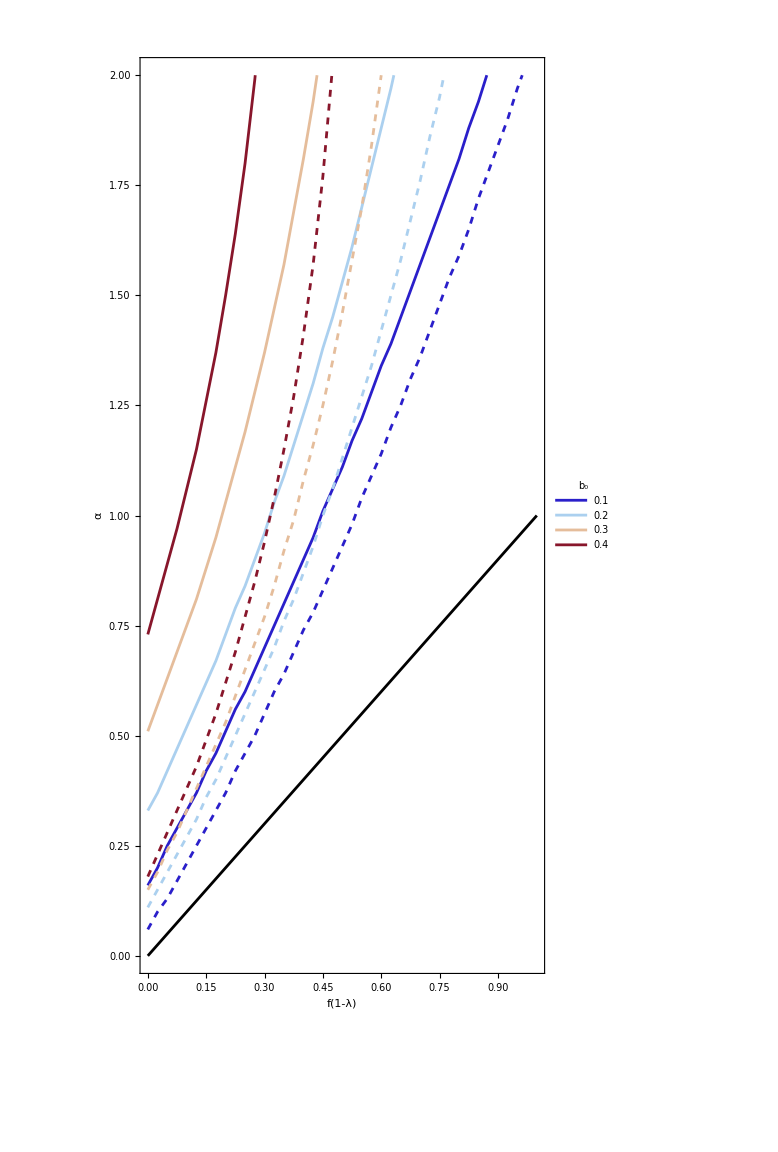

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideIceToeTrueStabilityBoundaryPlot_rho0.1.jpg

```mathematica
(*bvals=Join[{-0.2,-0.15,-0.1,-0.05},Subdivide[0.1,0.4,3]];*)
bvals=Subdivide[0.1,0.4,3];
roundedLabels = Round[bvals,0.01];
fvals=Range[0,1,0.025];  

(*Parallel computation of {f,alpha} pairs for each ρ,b value*)
ρvalue=0.1;
k1=0.5;
k2=1.5;
(*check if function works*)
xPosRoot[ρvalue,0.6,0.6,0.2,k1]
locusPosFun[0.6,0.2,k1,ρvalue]

data=ParallelTable[{f,locusPosFun[f,b,k1,ρvalue]},{b,bvals},{f,fvals}];
data2=ParallelTable[{f,locusPosFun[f,b,k2,ρvalue]},{b,bvals},{f,fvals}];
styles=Table[{ColorData["ThermometerColors"][r],Thick},{r,Rescale[Range[Length[bvals]]]}];
styles2=Table[{ColorData["ThermometerColors"][r],Dashed},{r,Rescale[Range[Length[bvals]]]}];
(*Plot each set of points as a line*)
p1=ListLinePlot[data,PlotRange->{0,2},PlotLegends->Placed[LineLegend[roundedLabels,LegendLabel->Style["b₀",Bold,20]],Right],
LabelStyle->{FontSize->20},
ImageSize->Large,PlotStyle->styles];
p2=ListLinePlot[data2,PlotRange->{0,2},PlotStyle->styles2];
p3=Plot[f,{f,0,1},PlotStyle->{Black,Thick}];

fig=Show[p1,p2,p3,FrameLabel->{"f(1-λ)","α"},Frame->True,LabelStyle->{FontSize->25},AspectRatio->2]
Export[NotebookDirectory[]<>"LandslideIceToeTrueStabilityBoundaryPlot_rho"<>ToString[ρvalue]<>".jpg",fig,"JPEG"]
```

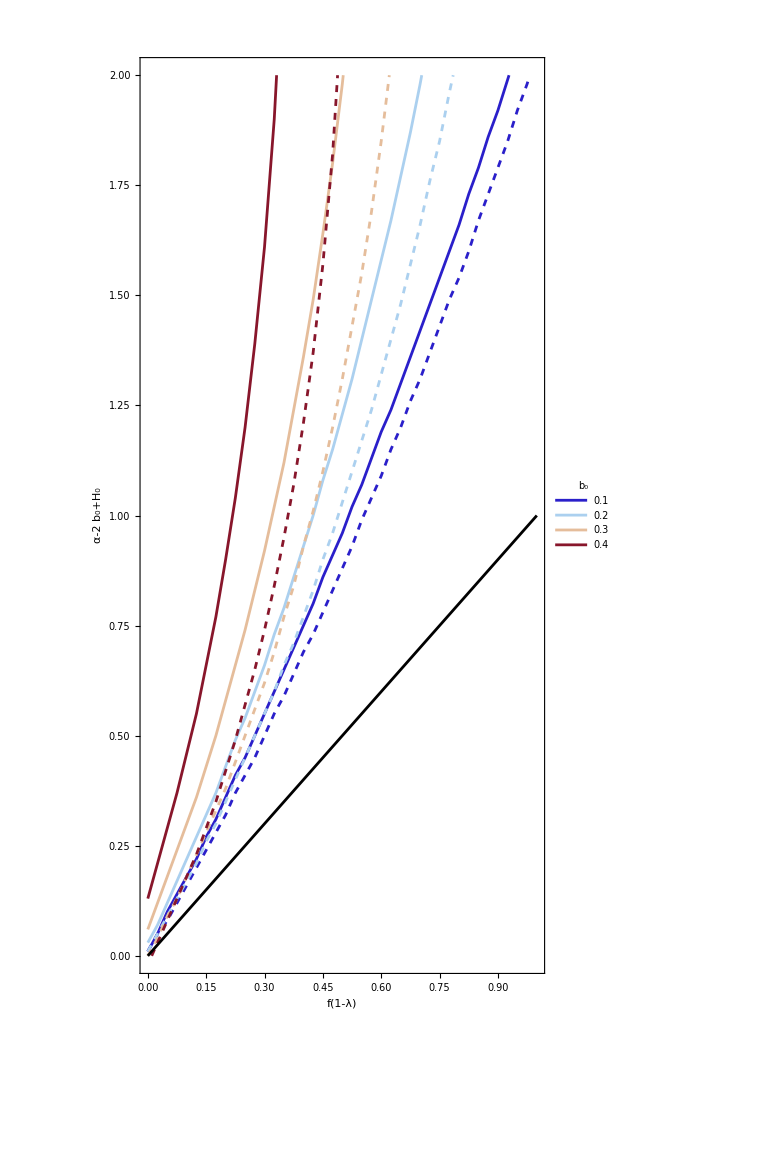

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideIceToeNormalizedStabilityBoundaryPlot_rho0.1.jpg

```mathematica
dataNorm=Table[With[{f=fvals[[i]],α=data[[j,i,2]],b=bvals[[j]]},{f,α-2 b+k1 b}],{j,Length[bvals]},{i,Length[fvals]}];
dataNorm2=Table[With[{f=fvals[[i]],α=data2[[j,i,2]],b=bvals[[j]]},{f,α-2 b+k2 b}],{j,Length[bvals]},{i,Length[fvals]}];
(*Plot each set of points as a line*)
p1=ListLinePlot[dataNorm,PlotRange->{0,2},PlotLegends->Placed[LineLegend[roundedLabels,LegendLabel->Style["b₀",Bold,20]],Right],
LabelStyle->{FontSize->20},
ImageSize->Large,PlotStyle->styles];
p2=ListLinePlot[dataNorm2,PlotRange->{0,2},PlotStyle->styles2];
p3=Plot[f,{f,0,1},PlotStyle->{Black,Thick}];

fig=Show[p1,p2,p3,FrameLabel->{Style["f(1-λ)",25],Style["α"+Subscript["H",0]-2 Subscript["b",0],25]},
Frame->True,LabelStyle->{FontSize->25},AspectRatio->2]
Export[NotebookDirectory[]<>"LandslideIceToeNormalizedStabilityBoundaryPlot_rho"<>ToString[ρvalue]<>".jpg",fig,"JPEG"]
```

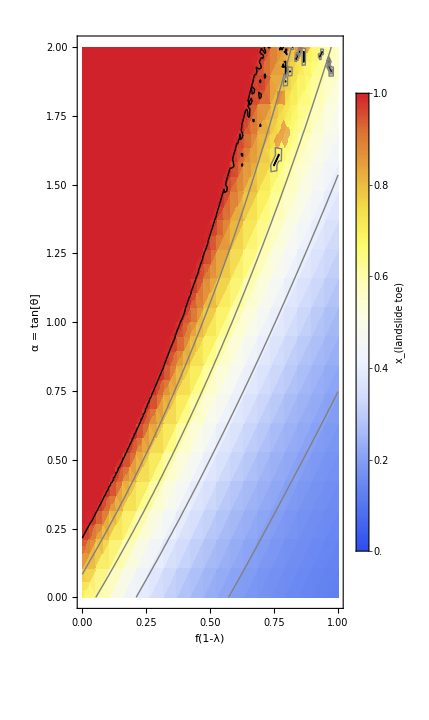

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideToeIceParameterPlot.jpg

```mathematica
(*define function to find landslide toe*)
ρvalue = 0.1;
xPosRoot[ρv_?NumericQ,αv_?NumericQ,fv_?NumericQ, b0_?NumericQ]:=Module[{sol,res},
xend=1.01;sol=Quiet@Check[NDSolve[{eqiceODE/.{ρ->ρv,bmax->b0,α->αv,fλ->fv},H[0]==Abs[b0],WhenEvent[H[x]<=0.0000001,{xend=x,"StopIntegration"}]},H,{x,0,1}],$Failed];
If[sol===$Failed,1.01,(*fallback if solve fails*)
res=xend
]
]
bplotval = 0.2;
contours={0,0.2,0.4,0.6,0.8,0.99};
dplot=DensityPlot[
Clip[xPosRoot[ρvalue,αv,fv,bplotval],{0,1.1}],(*clamp values to[0,1]*){fv,0,1},{αv,0,2},ColorFunction->(ColorData[{"Temperature",{0,1}}][#]&),ColorFunctionScaling->False,(*use actual values,not rescaled*)FrameLabel->{"f(1-λ)","α = tan[θ]"},PlotPoints->20,Mesh->False,PlotLegends->BarLegend[{ColorData[{"Temperature",{0,1}}],{0,1}},LegendLabel->Style[Subscript[x,"landslide toe"],FontSize->14]],ImageSize->Medium,LabelStyle->{FontSize->15}];

cplot=ContourPlot[xPosRoot[ρvalue,αv,fv,bplotval],{fv,0,1},{αv,0,2},Contours->contours,ContourStyle->{Gray,Gray,Gray,Gray,Gray,Directive[Black,Thick]},ContourShading->None];

fig=Show[dplot,cplot,AspectRatio->2]
Export[NotebookDirectory[]<>"LandslideToeIceParameterPlot.jpg",fig,"JPEG",ImageResolution->500]
```

## Plot profiles

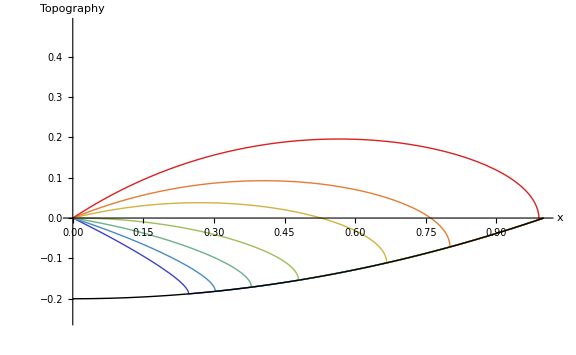

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideToeIceTopographicProfiles.jpg

```mathematica
fvval = 0.6;
bplotval = 0.2;
ρvalue = 0.1;
paramSets={
{0.1,fvval,bplotval},
{0.3,fvval,bplotval},
{0.5,fvval,bplotval},
{0.7,fvval,bplotval},
{1.0,fvval,bplotval},
{1.2,fvval,bplotval},
{1.5,fvval,bplotval}};
(*Number of parameter sets*)
nlines=Length[paramSets];
(*Hsol[αv_?NumericQ,fv_?NumericQ,b0_?NumericQ]:=
Quiet@Module[{bv,sol,H},
(*Define the profile bv[x] here if needed*)
bv[x_]:=b0*(x^2-1);
eqiceODE = (ρvalue-1)(D[H[x],x]+D[bv,x]) - 0.5*((αv-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*αv))*H[x]  -ρvalue*((Abs[b0]-b0) - H[x]-bv+ x*αv)*(fv/H[x]+D[bv,x,x]*(αv/(1+D[bv,x]*αv)-D[bv,x]/ (1+(D[bv,x])^2)))==fv + ρvalue *αv-(αv-D[bv,x])/(1+D[bv,x]*αv);
xendice=1.0;
sol = NDSolve[{eqiceODE,H[0]==Abs[b0],WhenEvent[H[x]<=0.0000001,{xendice=x,"StopIntegration"}]},H,{x,0,1.0}];
(*thickness has artifacts*)
Hsol= H[x]/.sol;
Hice[x_]:=Piecewise[{{Evaluate[Hsol],0<=x<=xendice }},0];
Function[x,Hice]
];*)
Hsol[αv_?NumericQ,fv_?NumericQ,b0_?NumericQ]:=Quiet@Module[{bv,sol,xendice,Hfun},(*Define basal profile*)bv[x_]:=b0*(x^2-1);
(*Define ODE*)eqiceODE=(ρvalue-1) (H'[x]+D[bv[x],x])-0.5*((αv-D[bv[x],x])/(1+(D[bv[x],x])^2)*D[bv[x],{x,2}]/(1+D[bv[x],x]*αv)) H[x]-ρvalue*((Abs[b0]-b0)-H[x]-bv[x]+x*αv)*(fv/H[x]+D[bv[x],{x,2}]*(αv/(1+D[bv[x],x]*αv)-D[bv[x],x]/(1+(D[bv[x],x])^2)))==fv+ρvalue*αv-(αv-D[bv[x],x])/(1+D[bv[x],x]*αv);
xendice=1.0;
(*Solve ODE with stopping condition*)sol=NDSolve[{eqiceODE,H[0]==Abs[b0],WhenEvent[H[x]<=10^-3,{xendice=x,"StopIntegration"}]},H,{x,0,1.0}];
(*Extract interpolating function*)
Hfun=First[H/. sol];
(*Define piecewise thickness function*)Function[x,Piecewise[{{Hfun[x],0<=x<=xendice}},0]]];
 
(*Generate a list of H[x]+b[x] and b[x] curves for each parameter set*)
curves = Table[Module[{Hf,αv,fv,b0,color},{αv,fv,b0}=
paramSets[[i]];
Hf=Hsol[αv,fv,b0];
color=ColorData["Rainbow"][i/nlines];(*gradient from blue to red*)
{Style[Hf[x]+bplotval*(x^2-1),color,Thick]}  (*dashed baseline*)],{i,nlines}];

(*Flatten the list so all curves are in a single list*)
curvesFlat=Flatten[curves,1];

(*Plot all curves together*)
fig=Plot[Evaluate[Join[curvesFlat,{Style[bplotval*(x^2-1),Black,Thick]}]],{x,0,1},
PlotRange->{-1.25*bplotval,2.4*bplotval},PlotLegends->None,Frame->None,AxesLabel->{"x","Topography"},LabelStyle->{FontSize->20},ImageSize->Large]
Export[NotebookDirectory[]<>"LandslideToeIceTopographicProfiles.jpg",fig,"JPEG",ImageResolution->500]
```